```mathematica
SetDirectory["~/mthesis/graphanalysis"]
```

/home/remco/Thesis/graphanalysis

```mathematica
data=Import["dep-growth-libmad"];
```

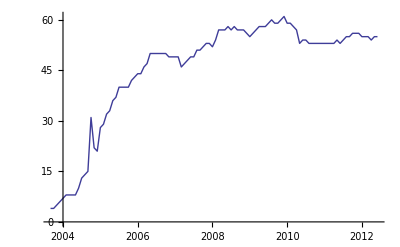

```mathematica
curvepoints=Select[{2000+#⟦1⟧/12,#⟦2⟧}&/@data,#⟦2⟧>0&]⟦1;;-1⟧;
ListLinePlot[curvepoints]
```

```mathematica
Bass[n_,p_,q_,t_]:=n(1-Exp[-(p+q)t])/(1+(q/p)Exp[-(p+q)t])
```

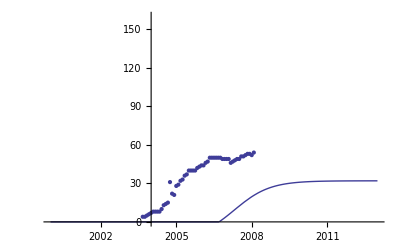

```mathematica
DataPointsPlot=Show[ListPlot[Take[curvepoints,54]],Plot[Max[0,Bass[32,0.42,1,t-2006.7]],{t,2000,2013},Frame->True],PlotRange->{0,160}]
```

```mathematica
nlm=NonlinearModelFit[curvepoints,{Bass[M,p,q,t-t0],q>0,p>0(*,q<=1,p<=1*)},{{t0,2003.4},{M,55.4},{p,0.177},{q,1.135}},t, MaxIterations->10000];
```

NonlinearModelFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 10000 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {1.68072, 7.57381, 0.884087}, is returned.

```mathematica
nlm["BestFit"]
```

(55.3786 (1-ⅇ^(-1.32297 (-2003.52+t))))/(1+5.68423 ⅇ^(-1.32297 (-2003.52+t)))

```mathematica
nlm["ParameterTable"]
```

FittedModel::constr: The property values {"ParameterTable"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
t0 | 2003.52 | 0.150261 | 13333.6 | 3.89548827391128×10^-320
M | 55.3786 | 0.386751 | 143.189 | 2.10604×10^-119
p | 0.197924 | 0.0666472 | 2.96972 | 0.00371619
q | 1.12504 | 0.170872 | 6.58413 | 2.01962×10^-9

```mathematica
nlm["ANOVATable"]
```

FittedModel::constr: The property values {"ANOVATable"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| DF | SS | MS
Model | 4 | 245108. | 61277.
Error | 102 | 768.127 | 7.53066
Uncorrected Total | 106 | 245876. | 
Corrected Total | 105 | 27066. |

```mathematica
nlm["ParameterConfidenceIntervalTable", ConfidenceLevel->.95]
```

FittedModel::constr: The property values {"ParameterConfidenceIntervalTable"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | Confidence Interval
t0 | 2003.52 | 0.150261 | {2003.22,2003.82}
M | 55.3786 | 0.386751 | {54.6115,56.1458}
p | 0.197924 | 0.0666472 | {0.0657291,0.330118}
q | 1.12504 | 0.170872 | {0.78612,1.46397}

```mathematica
nlm["AdjustedRSquared"]
```

0.996753

```mathematica
ConfidenceBands=Table[nlm["SinglePredictionBands",ConfidenceLevel->cl],{cl,{.90,.95,.99,.999}}];
```

FittedModel::constr: The property values {"SinglePredictionBands"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::stop: Further output of FittedModel :: constr will be suppressed during this calculation.

```mathematica
ConfidenceBandsPlot=Plot[ConfidenceBands,{t,2003,2013},
Filling->{1->{2},3->{4},5->{6},7->{8}},PlotStyle->{None},FillingStyle->{Directive[Red,Opacity[0.1]]},PlotRange->{0,800}];
```

```mathematica
ModelCurvePlot=Plot[nlm[t],{t,2003,2012.4},PlotStyle->RGBColor[0.5,0,0],PlotRange->{0,800}];
```

```mathematica
DataStalksPlot=ListPlot[{curvepoints,{#1,nlm[#1]}&/@curvepoints⟦1;;-1,1⟧},Filling->{1->{2}},PlotStyle->{None,None},FillingStyle->Directive[Black,Opacity[0.2]],PlotRange->{0,68}];
```

```mathematica
DataDotsPlot=ListPlot[curvepoints,PlotStyle->{Black},FillingStyle->Directive[Black,Opacity[0.2]]];
```

```mathematica
DataDotsPlot2=ListPlot[Take[curvepoints,-17],PlotStyle->{Blue},FillingStyle->Directive[Black,Opacity[0.2]]];
```

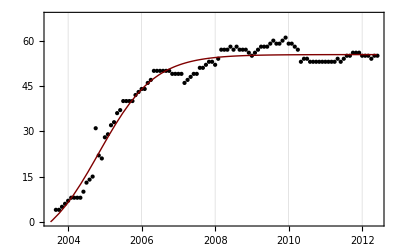

```mathematica
Show[(*ConfidenceBandsPlot,*)(*DataStalksPlot,*)DataDotsPlot,(*DataDotsPlot2,*)ModelCurvePlot,(*ListLinePlot[curvepoints,PlotStyle->RGBColor[0.5,0.5,0.5]],*)PlotRange->{0,68},GridLines->{Automatic,None},GridLinesStyle->Directive[Black,Opacity[0.2]],Frame->True,AxesOrigin->{2003,0}]
```

```mathematica
Export["BassFit-libmad-1.pdf",%,ImageSize->600]
```

BassFit-libmad-1.pdf

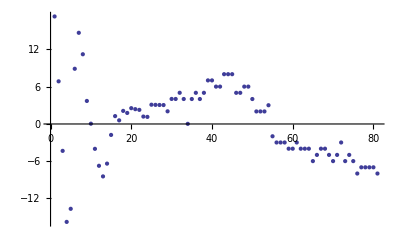

```mathematica
ListPlot[nlm["FitResiduals"]]
```

```mathematica
nlm["FitResiduals"]
```

{448.549,413.669,364.572,360.15,298.295,263.903,224.868,189.091,179.471,131.915,120.333,101.638,-489.246,-330.996,-345.734,-378.954,-500.667,-447.867,-360.538,-328.646,-313.141,-323.958,-460.013,-359.205,-229.416,-125.508,-204.325,-210.695,-193.426,-219.308,-219.117,-86.6109,-21.5331,-25.6134,205.431,288.894,243.079,166.296,137.863,160.1,214.33,158.876,119.058,98.1938,108.594,819.563,635.394,71.3713,56.7652,21.833,320.817,316.943,295.422,247.444,211.185,156.801,85.4293,307.19,287.185,221.498,175.197,142.33,136.932,109.022,83.6044,72.6696,55.1959,7.14941,-3.51438,-80.8499,-106.92,-69.7973,-234.559,-353.29,-408.081,-424.025,-501.222,-523.772,-521.78,-565.352,-582.593,-542.611,-537.515,-459.412,-479.408,-444.609,-349.12,-375.044,-316.481,-298.532,-206.293,-193.859,-192.321,-208.77,-162.293,-99.9731,-67.8928,-83.1309,3.23639,37.1357,108.496,187.25,243.331,377.677,372.228,387.925,380.713,435.54,191.354,190.106,227.751,308.244,356.543,380.607,443.398,511.879,590.015}